## Biharmonic Coordinates

Basic exmaple

```mathematica
colorBlue=0.5;
colorWhite=1;
colorBlack=0;
imgSize=302;
numBlocks=9;
blockSize=Quotient[imgSize,numBlocks];
border=2;
```

```mathematica
imgData=Module[{},
Table[
With[{blockI=Quotient[i-1,blockSize],blockJ=Quotient[j-1,blockSize]},
If[Mod[i-1-border,blockSize]==0||Mod[j-1-border,blockSize]==0||
Mod[i-border,blockSize]==0||Mod[j-border,blockSize]==0||
Mod[i+1-border,blockSize]==0||Mod[j+1-border,blockSize]==0,
If[blockI>4 &&blockJ==4&&j>blockJ*blockSize+border+1,colorWhite,colorBlack],
If[blockI≥4 &&blockJ==4,colorWhite,colorBlue]]],
{i,imgSize-border},{j,imgSize-border}]];
imgSize=Dimensions[imgData]⟦1;;2⟧;
```

```mathematica
Image[imgData]
```

-Graphics-

```mathematica
imgRaster=Raster[Reverse[imgData]];
```

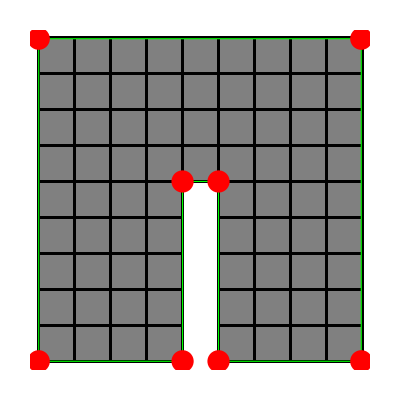

```mathematica
cntrlPts=
{{border,border},{border,imgSize⟦1⟧-border},{imgSize⟦1⟧,imgSize⟦2⟧}-{border,border},
{imgSize⟦1⟧-border,border},{5*blockSize+border,border},
{5*blockSize,5*blockSize}+{border,border},
{4*blockSize,5*blockSize}+{border,border},
{4*blockSize,0}+{border,border}
};
Show[Graphics[imgRaster],Graphics[{
{FaceForm[],EdgeForm[{Green,Thick,Dashed}],Polygon[cntrlPts]},
{Red,PointSize[.04],Point[cntrlPts]}
},imgSize+{10,10}]]
```

Tessellation

Hard example: Load image and build cage

```mathematica
SetDirectory[NotebookDirectory[]];
img=ImagePad[Image[Rasterize[Import["pikachu.png"],ImageSize->500]],20, White];
imgData=ImageData[img];
```

```mathematica
allpts={{195.29999999999998,440.99999999999994},{101.69999999999999,495.8999999999999},{24.300000000000004,509.3999999999999},{17.1,458.99999999999994},{104.39999999999998,374.4},{82.79999999999998,321.29999999999995},{100.79999999999998,275.4},{46.800000000000004,233.99999999999994},{67.5,179.09999999999997},{44.99999999999999,85.49999999999997},{33.300000000000004,34.19999999999999},{141.29999999999998,25.19999999999999},{188.09999999999997,39.599999999999966},{301.49999999999994,4.5},{359.09999999999997,35.99999999999997},{308.7,69.29999999999998},{367.19999999999993,147.59999999999997},{468.9,132.29999999999995},{536.4,214.19999999999996},{393.29999999999995,269.09999999999997},{372.59999999999997,313.19999999999993},{321.29999999999995,302.4},{340.2,363.59999999999997},{363.59999999999997,526.5},{306.9,537.3},{269.09999999999997,417.5999999999999}};
DynamicModule[{pts=allpts},
EventHandler[
Show[
Image[imgData],
Graphics[{
PointSize[.02],Green,Point[Dynamic[pts]],
FaceForm[],EdgeForm[{Red,Thick}],Polygon[Dynamic[pts]]}],
ImageSize->600,ImageMargins->50],
{{"MouseClicked",1}:> {
With[{mp=MousePosition["Graphics"]},
pts=Append[pts,mp];
allpts=pts]},
{"MouseClicked",2}:> {
pts=Most[pts];
allpts=pts}
}]]
```

Mean Value Coordinates

```mathematica
mvc[controls_][p_]:=
With[{len=Length[controls]},
Table[
With[{
pj=controls⟦j⟧,
pj1=controls⟦Mod[j,len]+1⟧,
pjm1=controls⟦Mod[j-2+len,len]+1⟧},
With[{
aj=VectorAngle[pj-p,pj1-p],
ajm1=VectorAngle[pjm1-p,pj-p]},
If[aj==Pi || ajm1==Pi,
Norm[pj-p]*1000,
(Tan[ajm1/2]+Tan[aj/2])/Norm[pj-p]]]],
{j,len}]];
```

```mathematica
f[cntrlPts_][npts_][x_]:=With[
{wgts=mvc[cntrlPts][x]},
Total[npts*(wgts//N)]/Total[wgts]]
```

```mathematica
polys=
With[{rimg=Reverse[imgData]},
Flatten[Table[
{{j,i},{j+1,i},{j+1,i+1},{j,i+1},rimg⟦i+1,j+1⟧},
{i,0,imgSize⟦1⟧-1},{j,0,imgSize⟦2⟧-1}],1]];
blackPolys=Select[polys,#⟦5⟧==0&]⟦All,1;;4⟧;
```

```mathematica
Graphics[{Black,Polygon[blackPolys⟦1000;;5000⟧]}]
```

```mathematica
cntrlPts
```

{{2,2},{2,298},{298,298},{298,2},{167,2},{167,167},{134,167},{134,2}}

```mathematica
SetOptions[$FrontEndSession,DynamicEvaluationTimeout->Infinity];
```

```mathematica
testPolys=blackPolys⟦1;;5000⟧;
border=5;
cpts2={{-border,-border},{-border,300+border},{300+border,300+border},{300+border,-border}};
g=f[cpts2];
DynamicModule[{npts=cpts2,selected=0,npolys=testPolys},
EventHandler[
Graphics[
{{FaceForm[],EdgeForm[{Blue,Dashed}],Polygon[cpts2],PointSize[.02],Point[cpts2]},
{FaceForm[],EdgeForm[{Red}],Polygon[Dynamic[npts]],PointSize[.02],Red,Point[Dynamic[npts]]},
{PointSize[.03],Blue,Point[testPt]},
{Black,Polygon[Dynamic[npolys]]},
{PointSize[.03],Red,Point[Dynamic[g[npts][testPt]]]}
},PlotRange->{{-50,350},{-50,350}}],
{{"MouseDown",1}:>
Module[{mp=MousePosition["Graphics"],best=5,dist},
selected=0;
Do[
dist=EuclideanDistance[mp,npts⟦i⟧];
If[dist<best,
best=dist;
selected=i],
{i,Length[npts]}]],
{"MouseDragged", 1}:>
If[selected>0,
npts⟦selected⟧=MousePosition["Graphics"]],
{"MouseUp",1}:>
With[{},
npolys=Map[g[npts],testPolys,{2}]]
}]]
```